坐标变换
三相静止坐标系ABC--两相静止坐标系αβ--两相旋转坐标系dq

1、三相静止坐标系ABC

```mathematica
U =220/220;
Um=Sqrt[2]*U;
a=Um*Cos[wt];
b=Um*Cos[wt-120*Pi/180];
c=Um*Cos[wt+120*Pi/180];
```

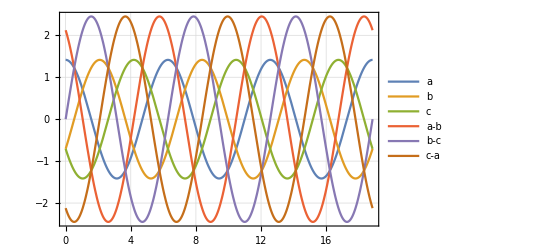

```mathematica
Plot[{a,b,c,a-b,b-c,c-a},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

```mathematica
ABC={{a},{b},{c}};
MatrixForm[ABC]
```

(√2 Cos[wt]
-√2 Sin[π/6-wt]
-√2 Sin[π/6+wt])

三相电压的相量表示
        在三相静止坐标系ABC中电压综合相量Uv为
                 U_v=u_A+u_B e^(j2π/3)+u_C e^(-j2π/3)=(3/2 U)_m e^jωt

```mathematica
Uv[wt_]= Um E^(I *wt)
```

√2 ⅇ^(ⅈ wt)

投影到三相静止坐标系ABC坐标轴上为

```mathematica
uva[wt_]=Um Cos[wt];
uvb[wt_]=Um Cos[2*Pi/3-wt];
uvc[wt_]=-Um Cos[wt+2*Pi/3-Pi];
```

旋转算子

```mathematica
rot=E^(I 2/3 Pi);
```

放到ABC坐标轴上表示为

```mathematica
Uva[wt_]=uva[wt];
Uvb[wt_]=uvb[wt]*rot;
Uvc[wt_]=uvc[wt]*rot^2;
```

三相静止坐标系的坐标轴ABC

```mathematica
AxisA=4*U;
AxisB=4*U*rot;
AxisC=4*U*rot^2;
```

```mathematica
Animate[Graphics[{
Thick,Red,Arrow[{{0,0},{Re[Uv[wt]],Im[Uv[wt]]}}],
Dashed,Yellow,Arrow[{{0,0},{Re[Uva[wt]],Im[Uva[wt]]}}],
Dashed,Green,Arrow[{{0,0},{Re[Uvb[wt]],Im[Uvb[wt]]}}],
Dashed,Red,Arrow[{{0,0},{Re[Uvc[wt]],Im[Uvc[wt]]}}],
Dotted,Yellow,Arrow[{{0,0},{Re[AxisA],Im[AxisA]}}],
Dotted,Green,Arrow[{{0,0},{Re[AxisB],Im[AxisB]}}],
Dotted,Red,Arrow[{{0,0},{Re[AxisC],Im[AxisC]}}]},
Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium],{wt,0,2*Pi},AnimationRunning->False]
```

## 2、三相静止坐标系ABC-两相静止坐标系αβ

Clark变换就是三相静止坐标系ABC到两相静止坐标系αβ的变换

        Clark变换有等功率变换和等幅值变换，二者只是系数不同。以下是等功率变换：
                                  [α
β]=√(2/3)[1 | -1/2 | -1/2
0 | (√3)/2 | -(√3)/2][a
b
c]

```mathematica
ABC2AB=Sqrt[2/3]*{{1,-1/2,-1/2},{0,Sqrt[3]/2,-Sqrt[3]/2}};
MatrixForm[ABC2AB]
```

(√(2/3) | -1/(√6) | -1/(√6)
0 | 1/(√2) | -1/(√2))

通过Clark变换（等功率）从ABC坐标系变换到αβ坐标系

```mathematica
AB=ABC2AB.ABC;
MatrixForm[AB]
```

((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3)
-Sin[π/6-wt]+Sin[π/6+wt])

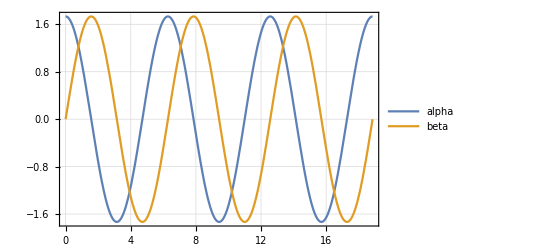

```mathematica
alpha=AB[[1,1]];
beta=AB[[2,1]];
Plot[{alpha,beta},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 3、两相静止坐标系αβ-两相旋转坐标系dq

两相静止坐标系αβ到两相旋转坐标系的变换，φ是d轴和α轴之间的夹角

        变换如下
                                     [d
q]=[cosφ | sinφ
-sinφ | cosφ][α
β]

```mathematica
AB2DQ={{Cos[wt],Sin[wt]},{-Sin[wt],Cos[wt]}};
MatrixForm[AB2DQ]
```

(Cos[wt] | Sin[wt]
-Sin[wt] | Cos[wt])

```mathematica
DQ=AB2DQ.AB
```

{{Sin[wt] (-Sin[π/6-wt]+Sin[π/6+wt])+Cos[wt] ((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3))},{Cos[wt] (-Sin[π/6-wt]+Sin[π/6+wt])-Sin[wt] ((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3))}}

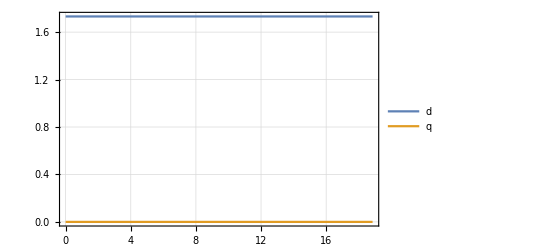

```mathematica
d=DQ[[1,1]];
q=DQ[[2,1]];
Plot[{d,q},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

4、三相静止坐标系ABC到两相旋转坐标系dq的变换

三相静止坐标系ABC到两相旋转坐标系dq的变换如下

[d
q]=√(2/3)[cosφ | -1/2cosφ+(√3)/2 sinφ | -1/2cosφ-(√3)/2 sinφ
-sinφ | 1/2 sinφ+(√3)/2 cosφ | 1/2 sinφ-(√3)/2 cosφ][a
b
c]=√(2/3)[cosφ | cos(φ-(2π)/3) | cos(φ+(2π)/3)
-sinφ | -sin(φ-(2π)/3) | -sin(φ+(2π)/3)][a
b
c]

```mathematica
ABC2DQZ=Sqrt[2/3]{{Cos[wt], -1/2 Cos[wt]+Sqrt[3]/2 Sin[wt], -1/2Cos[wt]-Sqrt[3]/2 Sin[wt]},{-Sin[wt], 1/2 Sin[wt]+Sqrt[3]/2 Cos[wt], 1/2 Sin[wt]-Sqrt[3]/2 Cos[wt]},{1/2, 1/2, 1/2}};
MatrixForm[ABC2DQZ]
```

(√(2/3) Cos[wt] | √(2/3) (-Cos[wt]/2+1/2 √3 Sin[wt]) | √(2/3) (-Cos[wt]/2-1/2 √3 Sin[wt])
-√(2/3) Sin[wt] | √(2/3) (1/2 √3 Cos[wt]+Sin[wt]/2) | √(2/3) (-1/2 √3 Cos[wt]+Sin[wt]/2)
1/(√6) | 1/(√6) | 1/(√6))

```mathematica
DQZ=ABC2DQZ.ABC;
```

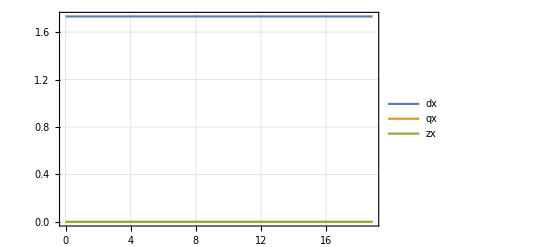

```mathematica
dx=DQZ[[1,1]];
qx=DQZ[[2,1]];
zx=DQZ[[3,1]];
Plot[{dx,qx,zx},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRange->Full]
```

5、两相静止坐标系αβ-三相静止坐标系ABC
        αβ坐标系变换为ABC坐标系，即三相静止变换为两相静止坐标系，称为逆Clark变换，下面是等功率逆Clark变换
                  [a
b
c]=√(2/3)[1 | 0
-1/2 | (√3)/2
-1/2 | -(√3)/2][α
β]

```mathematica
AB2ABC=Sqrt[2/3]*{{1,0},{-1/2,Sqrt[3]/2},{-1/2,-Sqrt[3]/2}};
MatrixForm[AB2ABC]
```

(√(2/3) | 0
-1/(√6) | 1/(√2)
-1/(√6) | -1/(√2))

```mathematica
ABC2=AB2ABC.AB;
MatrixForm[ABC2]
```

(√(2/3) ((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3))
(-Sin[π/6-wt]+Sin[π/6+wt])/(√2)-((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3))/(√6)
-(-Sin[π/6-wt]+Sin[π/6+wt])/(√2)-((2 Cos[wt])/(√3)+Sin[π/6-wt]/(√3)+Sin[π/6+wt]/(√3))/(√6))

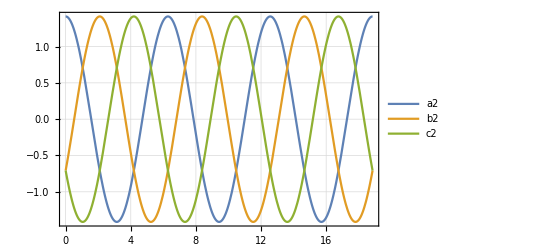

```mathematica
a2=ABC2[[1,1]];
b2=ABC2[[2,1]];
c2=ABC2[[3,1]];
Plot[{a2,b2,c2},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

6、两相旋转坐标系dq-两相静止坐标系αβ
        两相旋转坐标系dq到两相静止坐标系αβ的变换，φ是d轴和α轴之间的夹角
        
                        [α
β]=[cosφ | -sinφ
sinφ | cosφ][d
q]